```mathematica
ClearAll["Global`*"]
```

```mathematica
E2a[n_,k_, a_]:= E2a[n,k,a]=Sum[ E2a[n/j,k-1,a],{j,2,n}]-a Sum[ E2a[n/(a j),k-1,a],{j,1,n/a}];E2a[n_,0,a_]:=1
lin[n_,b_]:=Sum[(-1)^(k+1)/k E2a[n,k,b],{k,1,Log[2,n]}]
E2ax[n_,k_, a_,c_]:= E2ax[n,k,a,c]=Sum[ E2ax[n/j,k-1,a,c],{j,2,n}]-a^c Sum[ E2ax[n/(a j),k-1,a,c],{j,1,n/a}];E2ax[n_,0,a_,c_]:=1
linx[n_,b_,c_]:=Sum[(-1)^(k+1)/k E2a[n,k,b],{k,1,Log[2,n]}]
E2ay[n_,k_, a_,c_]:= E2ay[n,k,a,c]=Sum[ E2ay[n/j,k-1,a,c],{j,2,n}]+a^c Sum[ E2ay[n/(a j),k-1,a,c],{j,1,n/a}];E2ay[n_,0,a_,c_]:=1
liny[n_,b_,c_]:=Sum[(-1)^(k+1)/k E2a[n,k,b],{k,1,Log[2,n]}]
$RecursionLimit=10000
```

10000

```mathematica
lin[100,2]
```

4/5

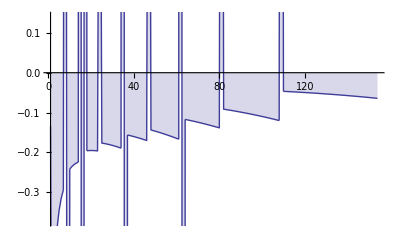

10000

```mathematica
DiscretePlot[(-1)^(k+1)/k E2a[10,k,1.015],{k,1,Log[1.015,10]}]
```

```mathematica
DiscretePlot[(-1)^(k+1)/k E2ax[10,k,1.015,1],{k,1,Log[1.015,10]}]
```

-Graphics-

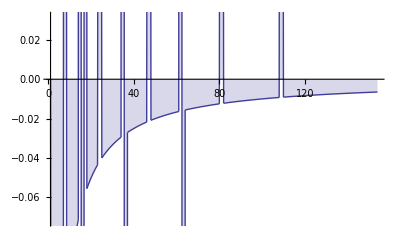

```mathematica
DiscretePlot[(-1)^(k+1)/k E2ax[10,k,1.015,0],{k,1,Log[1.015,10]}]
```

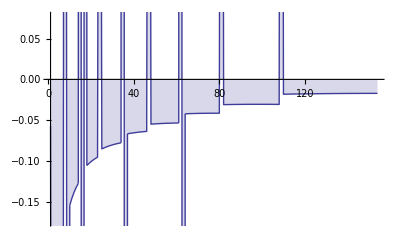

```mathematica
DiscretePlot[(-1)^(k+1)/k E2ax[10,k,1.015,1-EulerGamma],{k,1,Log[1.015,10]}]
```

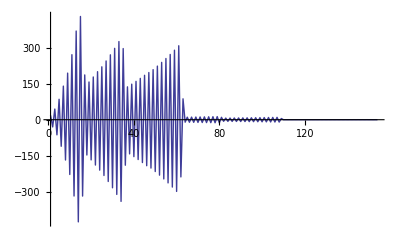

```mathematica
DiscretePlot[(-1)^(k+1)/k E2ay[10,k,1.015,1],{k,1,Log[1.015,10]}]
```

```mathematica
pp[k_,a_]:=(-1)^(k+1)/k E2ax[10,k,1.015,a]
pp2[k_,a_]:=(-1)^(k+1)/k E2ay[10,k,1.015,a]
```

```mathematica
Table[{1.015^k,pp[k,1],pp[k,0], pp[k,1/2]},{k,1,Log[1.015,10]}]//TableForm
```

1.015 | -0.135 | 0. | -0.0672488
1.03022 | -1.63759 | -1.5 | -1.56789
1.04568 | -0.473558 | -0.333333 | -0.401872
1.06136 | -0.392912 | -0.25 | -0.319193
1.07728 | -0.345651 | -0.2 | -0.269854
1.09344 | -0.315108 | -0.166667 | -0.237188
1.10984 | -0.294143 | -0.142857 | -0.214051
1.12649 | 4.79003 | 4.375 | 4.57926
1.14339 | -4.68973 | -4.11111 | -4.38947
1.16054 | -0.241858 | -0.1 | -0.164996
1.17795 | -0.235432 | -0.0909091 | -0.156513
1.19562 | -0.230571 | -0.0833333 | -0.14955
1.21355 | -0.226927 | -0.0769231 | -0.143759
1.23176 | -0.224252 | -0.0714286 | -0.13889
1.25023 | 56.4548 | 45.2667 | 50.5542
1.26899 | -105.534 | -85.0625 | -94.7468
1.28802 | 49.0735 | 39.9412 | 44.275
1.30734 | -0.195833 | -0.0555556 | -0.116006
1.32695 | -0.195325 | -0.0526316 | -0.1136
1.34686 | -0.195152 | -0.05 | -0.11149
1.36706 | -0.195272 | -0.047619 | -0.109636
1.38756 | -0.195652 | -0.0454545 | -0.108003
1.40838 | -0.196265 | -0.0434783 | -0.106562
1.4295 | 1.23242 | 0.958333 | 1.09033
1.45095 | -0.176658 | -0.04 | -0.0952362
1.47271 | -0.177525 | -0.0384615 | -0.0941809
1.4948 | -0.178548 | -0.037037 | -0.0932439
1.51722 | -0.179717 | -0.0357143 | -0.092413
1.53998 | -0.18102 | -0.0344828 | -0.0916776
1.56308 | -0.182451 | -0.0333333 | -0.0910287
1.58653 | -0.184002 | -0.0322581 | -0.0904584
1.61032 | -0.185666 | -0.03125 | -0.0899598
1.63448 | -0.187438 | -0.030303 | -0.0895269
1.659 | -0.189315 | -0.0294118 | -0.0891541
1.68388 | 58.7446 | 34.9714 | 45.3287
1.70914 | -58.2199 | -35.0278 | -45.1571
1.73478 | -0.156254 | -0.027027 | -0.0759759
1.7608 | -0.157538 | -0.0263158 | -0.0756363
1.78721 | -0.15889 | -0.025641 | -0.0753362
1.81402 | -0.160309 | -0.025 | -0.0750728
1.84123 | -0.161792 | -0.0243902 | -0.0748436
1.86885 | -0.163337 | -0.0238095 | -0.0746466
1.89688 | -0.164944 | -0.0232558 | -0.0744796
1.92533 | -0.166611 | -0.0227273 | -0.0743409
1.95421 | -0.168336 | -0.0222222 | -0.0742288
1.98353 | -0.17012 | -0.0217391 | -0.0741418
2.01328 | 1.84132 | 0.978723 | 1.34482
2.04348 | -0.143658 | -0.0208333 | -0.0634356
2.07413 | -0.145157 | -0.0204082 | -0.0633369
2.10524 | -0.146705 | -0.02 | -0.0632578
2.13682 | -0.148301 | -0.0196078 | -0.0631975
2.16887 | -0.149945 | -0.0192308 | -0.0631549
2.20141 | -0.151636 | -0.0188679 | -0.0631292
2.23443 | -0.153373 | -0.0185185 | -0.0631197
2.26794 | -0.155158 | -0.0181818 | -0.0631257
2.30196 | -0.156989 | -0.0178571 | -0.0631465
2.33649 | -0.158867 | -0.0175439 | -0.0631815
2.37154 | -0.160792 | -0.0172414 | -0.0632302
2.40711 | -0.162763 | -0.0169492 | -0.0632919
2.44322 | -0.164782 | -0.0166667 | -0.0633663
2.47987 | -0.166846 | -0.0163934 | -0.0634528
2.51707 | 79.1186 | 31.4839 | 49.912
2.55482 | -76.992 | -31.0159 | -48.8666
2.59314 | -0.117163 | -0.015625 | -0.0490478
2.63204 | -0.118287 | -0.0153846 | -0.0490243
2.67152 | -0.119439 | -0.0151515 | -0.0490096
2.7116 | -0.120617 | -0.0149254 | -0.0490034
2.75227 | -0.121822 | -0.0147059 | -0.0490054
2.79355 | -0.123054 | -0.0144928 | -0.0490154
2.83546 | -0.124313 | -0.0142857 | -0.049033
2.87799 | -0.125599 | -0.0140845 | -0.0490581
2.92116 | -0.126911 | -0.0138889 | -0.0490903
2.96498 | -0.128251 | -0.0136986 | -0.0491295
3.00945 | -0.129618 | -0.0135135 | -0.0491754
3.05459 | -0.131011 | -0.0133333 | -0.049228
3.10041 | -0.132433 | -0.0131579 | -0.0492869
3.14692 | -0.133881 | -0.012987 | -0.049352
3.19412 | -0.135358 | -0.0128205 | -0.0494232
3.24203 | -0.136862 | -0.0126582 | -0.0495003
3.29066 | -0.138394 | -0.0125 | -0.0495832
3.34002 | 3.20007 | 0.987654 | 1.7779
3.39012 | -0.0914433 | -0.0121951 | -0.0361098
3.44097 | -0.0923094 | -0.0120482 | -0.0361071
3.49259 | -0.0931931 | -0.0119048 | -0.0361088
3.54498 | -0.0940945 | -0.0117647 | -0.0361149
3.59815 | -0.0950137 | -0.0116279 | -0.0361253
3.65213 | -0.0959507 | -0.0114943 | -0.0361398
3.70691 | -0.0969058 | -0.0113636 | -0.0361583
3.76251 | -0.097879 | -0.011236 | -0.0361808
3.81895 | -0.0988704 | -0.0111111 | -0.0362072
3.87623 | -0.0998802 | -0.010989 | -0.0362374
3.93438 | -0.100908 | -0.0108696 | -0.0362712
3.99339 | -0.101955 | -0.0107527 | -0.0363087
4.05329 | -0.103021 | -0.0106383 | -0.0363497
4.11409 | -0.104106 | -0.0105263 | -0.0363942
4.1758 | -0.105209 | -0.0104167 | -0.036442
4.23844 | -0.106332 | -0.0103093 | -0.0364932
4.30202 | -0.107475 | -0.0102041 | -0.0365477
4.36655 | -0.108637 | -0.010101 | -0.0366054
4.43205 | -0.109819 | -0.01 | -0.0366663
4.49853 | -0.111021 | -0.00990099 | -0.0367303
4.566 | -0.112243 | -0.00980392 | -0.0367973
4.63449 | -0.113485 | -0.00970874 | -0.0368674
4.70401 | -0.114748 | -0.00961538 | -0.0369404
4.77457 | -0.116032 | -0.00952381 | -0.0370163
4.84619 | -0.117337 | -0.00943396 | -0.0370951
4.91888 | -0.118664 | -0.00934579 | -0.0371767
4.99267 | -0.120012 | -0.00925926 | -0.0372611
5.06756 | 4.94618 | 0.990826 | 2.21378
5.14357 | -0.0467597 | -0.00909091 | -0.0206177
5.22072 | -0.0470335 | -0.00900901 | -0.0205846
5.29903 | -0.0473128 | -0.00892857 | -0.0205532
5.37852 | -0.0475975 | -0.00884956 | -0.0205236
5.4592 | -0.0478877 | -0.00877193 | -0.0204955
5.54109 | -0.0481834 | -0.00869565 | -0.0204691
5.6242 | -0.0484845 | -0.00862069 | -0.0204443
5.70856 | -0.0487912 | -0.00854701 | -0.020421
5.79419 | -0.0491033 | -0.00847458 | -0.0203993
5.88111 | -0.0494211 | -0.00840336 | -0.020379
5.96932 | -0.0497444 | -0.00833333 | -0.0203602
6.05886 | -0.0500732 | -0.00826446 | -0.0203428
6.14975 | -0.0504078 | -0.00819672 | -0.0203268
6.24199 | -0.0507479 | -0.00813008 | -0.0203122
6.33562 | -0.0510937 | -0.00806452 | -0.0202989
6.43066 | -0.0514452 | -0.008 | -0.020287
6.52712 | -0.0518025 | -0.00793651 | -0.0202764
6.62502 | -0.0521655 | -0.00787402 | -0.020267
6.7244 | -0.0525344 | -0.0078125 | -0.0202589
6.82526 | -0.052909 | -0.00775194 | -0.0202521
6.92764 | -0.0532896 | -0.00769231 | -0.0202465
7.03156 | -0.053676 | -0.00763359 | -0.020242
7.13703 | -0.0540684 | -0.00757576 | -0.0202388
7.24409 | -0.0544668 | -0.0075188 | -0.0202367
7.35275 | -0.0548713 | -0.00746269 | -0.0202358
7.46304 | -0.0552818 | -0.00740741 | -0.020236
7.57498 | -0.0556984 | -0.00735294 | -0.0202373
7.68861 | -0.0561212 | -0.00729927 | -0.0202397
7.80394 | -0.0565503 | -0.00724638 | -0.0202431
7.921 | -0.0569856 | -0.00719424 | -0.0202477
8.03981 | -0.0574272 | -0.00714286 | -0.0202533
8.16041 | -0.0578752 | -0.0070922 | -0.0202599
8.28282 | -0.0583297 | -0.00704225 | -0.0202675
8.40706 | -0.0587906 | -0.00699301 | -0.0202762
8.53316 | -0.0592581 | -0.00694444 | -0.0202858
8.66116 | -0.0597321 | -0.00689655 | -0.0202964
8.79108 | -0.0602129 | -0.00684932 | -0.0203081
8.92294 | -0.0607003 | -0.00680272 | -0.0203206
9.05679 | -0.0611945 | -0.00675676 | -0.0203341
9.19264 | -0.0616956 | -0.00671141 | -0.0203486
9.33053 | -0.0622035 | -0.00666667 | -0.0203639
9.47049 | -0.0627185 | -0.00662252 | -0.0203802
9.61255 | -0.0632404 | -0.00657895 | -0.0203974
9.75673 | -0.0637695 | -0.00653595 | -0.0204155
9.90308 | -0.0643057 | -0.00649351 | -0.0204345

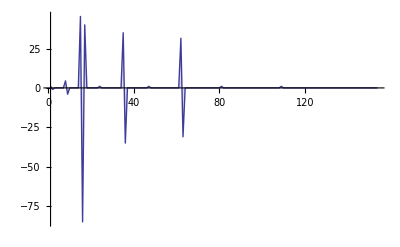

```mathematica
DiscretePlot[((-1)^(k+1) E2ax[10,k,1.015,0]+1)/k,{k,1,Log[1.015,10]}]
```

```mathematica
Table[{10/1.015^k,((-1)^(k+1) E2ax[10,k,1.015,0]+1)/k},{k,1,Log[1.015,10]}]//TableForm
```

9.85222 | 1.
9.70662 | -1.
9.56317 | 0.
9.42184 | 0.
9.2826 | 0.
9.14542 | 0.
9.01027 | 0.
8.87711 | 4.5
8.74592 | -4.
8.61667 | 0.
8.48933 | 0.
8.36387 | 0.
8.24027 | 0.
8.11849 | 0.
7.99852 | 45.3333
7.88031 | -85.
7.76385 | 40.
7.64912 | 0.
7.53607 | 0.
7.4247 | 0.
7.31498 | 0.
7.20688 | 0.
7.10037 | 0.
6.99544 | 1.
6.89206 | 0.
6.79021 | 0.
6.68986 | 0.
6.59099 | 0.
6.49359 | 0.
6.39762 | 0.
6.30308 | 0.
6.20993 | 0.
6.11816 | 0.
6.02774 | 0.
5.93866 | 35.
5.8509 | -35.
5.76443 | 0.
5.67924 | 0.
5.59531 | 0.
5.51262 | 0.
5.43116 | 0.
5.35089 | 0.
5.27182 | 0.
5.19391 | 0.
5.11715 | 0.
5.04153 | 0.
4.96702 | 1.
4.89362 | 0.
4.8213 | 0.
4.75005 | 0.
4.67985 | 0.
4.61069 | 0.
4.54255 | 0.
4.47542 | 0.
4.40928 | 0.
4.34412 | 0.
4.27992 | 0.
4.21667 | 0.
4.15435 | 0.
4.09296 | 0.
4.03247 | 0.
3.97288 | 31.5
3.91417 | -31.
3.85632 | 0.
3.79933 | 0.
3.74318 | 0.
3.68787 | 0.
3.63337 | 0.
3.57967 | 0.
3.52677 | 0.
3.47465 | 0.
3.4233 | 0.
3.37271 | 0.
3.32287 | 0.
3.27376 | 0.
3.22538 | 0.
3.17771 | 0.
3.13075 | 0.
3.08448 | 0.
3.0389 | 0.
2.99399 | 1.
2.94975 | 0.
2.90615 | 0.
2.86321 | 0.
2.82089 | 0.
2.7792 | 0.
2.73813 | 0.
2.69767 | 0.
2.6578 | 0.
2.61852 | 0.
2.57982 | 0.
2.5417 | 0.
2.50414 | 0.
2.46713 | 0.
2.43067 | 0.
2.39475 | 0.
2.35936 | 0.
2.32449 | 0.
2.29014 | 0.
2.25629 | 0.
2.22295 | 0.
2.1901 | 0.
2.15773 | 0.
2.12585 | 0.
2.09443 | 0.
2.06348 | 0.
2.03298 | 0.
2.00294 | 0.
1.97334 | 1.
1.94417 | 0.
1.91544 | 0.
1.88714 | 0.
1.85925 | 0.
1.83177 | 0.
1.8047 | 0.
1.77803 | 0.
1.75175 | 0.
1.72587 | 0.
1.70036 | 0.
1.67523 | 0.
1.65047 | 0.
1.62608 | 0.
1.60205 | 0.
1.57838 | 0.
1.55505 | 0.
1.53207 | 0.
1.50943 | 0.
1.48712 | 0.
1.46514 | 0.
1.44349 | 0.
1.42216 | 0.
1.40114 | 0.
1.38044 | 0.
1.36004 | 0.
1.33994 | 0.
1.32013 | 0.
1.30063 | 0.
1.2814 | 0.
1.26247 | 0.
1.24381 | 0.
1.22543 | 0.
1.20732 | 0.
1.18948 | 0.
1.1719 | 0.
1.15458 | 0.
1.13752 | 0.
1.12071 | 0.
1.10414 | 0.
1.08783 | 0.
1.07175 | 0.
1.05591 | 0.
1.04031 | 0.
1.02493 | 0.
1.00979 | 0.

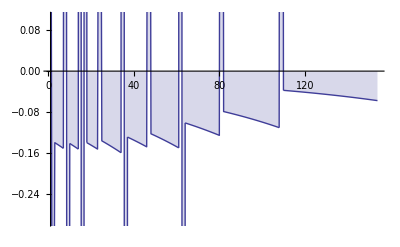

```mathematica
DiscretePlot[((-1)^(k+1) E2ax[10,k,1.015,1]+1 )/k,{k,1,Log[1.015,10]}]
```

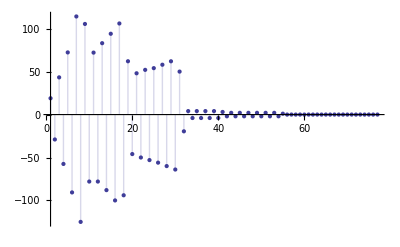

```mathematica
DiscretePlot[((-1)^(k+1) E2ay[10,k,1.03,0]+1)/k,{k,1,Log[1.03,10]}]
```

```mathematica
Table[{10/1.03^k,((-1)^(k+1) E2ay[10,k,1.03,0]+1)/k},{k,1,Log[1.03,10]}]//TableForm
```

9.70874 | 19.
9.42596 | -29.
9.15142 | 43.3333
8.88487 | -57.5
8.62609 | 72.4
8.37484 | -90.6667
8.13092 | 114.286
7.89409 | -125.
7.66417 | 105.556
7.44094 | -78.
7.22421 | 72.1818
7.0138 | -78.
6.80951 | 83.1538
6.61118 | -88.
6.41862 | 94.1333
6.23167 | -100.
6.05016 | 106.118
5.87395 | -94.
5.70286 | 62.1053
5.53676 | -46.
5.37549 | 48.0952
5.21893 | -50.
5.06692 | 52.087
4.91934 | -53.
4.77606 | 54.08
4.63695 | -56.
4.50189 | 58.0741
4.37077 | -60.
4.24346 | 62.069
4.11987 | -64.
3.99987 | 50.0645
3.88337 | -19.5
3.77026 | 4.06061
3.66045 | -4.
3.55383 | 4.05714
3.45032 | -4.
3.34983 | 4.05405
3.25226 | -4.
3.15754 | 4.05128
3.06557 | -4.
2.97628 | 3.04878
2.88959 | -2.
2.80543 | 2.04651
2.72372 | -2.
2.64439 | 2.04444
2.56737 | -2.
2.49259 | 2.04255
2.41999 | -2.
2.3495 | 2.04082
2.28107 | -2.
2.21463 | 2.03922
2.15013 | -2.
2.0875 | 2.03774
2.0267 | -2.
1.96767 | 1.03636
1.91036 | 0.
1.85472 | 0.0350877
1.8007 | 0.
1.74825 | 0.0338983
1.69733 | 0.
1.64789 | 0.0327869
1.5999 | 0.
1.5533 | 0.031746
1.50806 | 0.
1.46413 | 0.0307692
1.42149 | 0.
1.38009 | 0.0298507
1.33989 | 0.
1.30086 | 0.0289855
1.26297 | 0.
1.22619 | 0.028169
1.19047 | 0.
1.1558 | 0.0273973
1.12214 | 0.
1.08945 | 0.0266667
1.05772 | 0.
1.02691 | 0.025974